## Задание №1

Данные

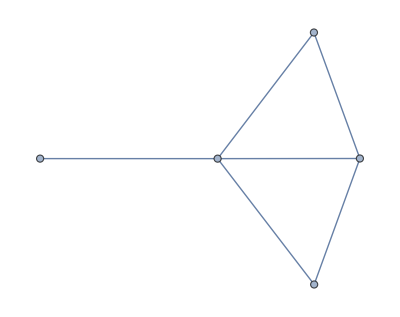

```mathematica
g=RandomGraph[{5,6}]
```

```mathematica
V=VertexList[g]
```

{1,2,3,4,5}

```mathematica
edgeList=EdgeList[g]
```

{1<->2,1<->5,2<->4,2<->5,3<->5,4<->5}

```mathematica
H=Max[VertexDegree[g]]+1(* оценка для H *)
```

5

```mathematica
c=RandomSample[edgeList,Round[0.1 Length[edgeList]]]
```

{1<->5}

```mathematica
d=Complement[edgeList,c]
```

{1<->2,2<->4,2<->5,3<->5,4<->5}

Переменные

```mathematica
xVars=Array[x,{Length[V],H}]
```

{{x[1,1],x[1,2],x[1,3],x[1,4],x[1,5]},{x[2,1],x[2,2],x[2,3],x[2,4],x[2,5]},{x[3,1],x[3,2],x[3,3],x[3,4],x[3,5]},{x[4,1],x[4,2],x[4,3],x[4,4],x[4,5]},{x[5,1],x[5,2],x[5,3],x[5,4],x[5,5]}}

```mathematica
etaVars=Array[η,{H}]
```

{η[1],η[2],η[3],η[4],η[5]}

```mathematica
etaCVars=Outer[ηc,c,Range[H]]
```

{{ηc[1<->5,1],ηc[1<->5,2],ηc[1<->5,3],ηc[1<->5,4],ηc[1<->5,5]}}

Целевая функция

```mathematica
of=Total[etaVars]
```

η[1]+η[2]+η[3]+η[4]+η[5]

Ограничения

```mathematica
con1=Thread[Total[Transpose[xVars]]==1]
```

{x[1,1]+x[1,2]+x[1,3]+x[1,4]+x[1,5]==1,x[2,1]+x[2,2]+x[2,3]+x[2,4]+x[2,5]==1,x[3,1]+x[3,2]+x[3,3]+x[3,4]+x[3,5]==1,x[4,1]+x[4,2]+x[4,3]+x[4,4]+x[4,5]==1,x[5,1]+x[5,2]+x[5,3]+x[5,4]+x[5,5]==1}

```mathematica
con2=Flatten[Table[Thread[Total[Select[#,MemberQ[i,#⟦1⟧]&]&/@Transpose[xVars],{2}]<=1],{i,d}]]
```

{x[1,1]+x[2,1]≤1,x[1,2]+x[2,2]≤1,x[1,3]+x[2,3]≤1,x[1,4]+x[2,4]≤1,x[1,5]+x[2,5]≤1,x[2,1]+x[4,1]≤1,x[2,2]+x[4,2]≤1,x[2,3]+x[4,3]≤1,x[2,4]+x[4,4]≤1,x[2,5]+x[4,5]≤1,x[2,1]+x[5,1]≤1,x[2,2]+x[5,2]≤1,x[2,3]+x[5,3]≤1,x[2,4]+x[5,4]≤1,x[2,5]+x[5,5]≤1,x[3,1]+x[5,1]≤1,x[3,2]+x[5,2]≤1,x[3,3]+x[5,3]≤1,x[3,4]+x[5,4]≤1,x[3,5]+x[5,5]≤1,x[4,1]+x[5,1]≤1,x[4,2]+x[5,2]≤1,x[4,3]+x[5,3]≤1,x[4,4]+x[5,4]≤1,x[4,5]+x[5,5]≤1}

```mathematica
con3=Thread[Total[etaCVars,{2}]<=1]
```

{ηc[1<->5,1]+ηc[1<->5,2]+ηc[1<->5,3]+ηc[1<->5,4]+ηc[1<->5,5]≤1}

```mathematica
con4=Join[Thread[x@@{#[[1,1]],#[[2]]}&/@Flatten[etaCVars]<=Flatten[etaCVars]],Thread[x@@{#[[1,2]],#[[2]]}&/@Flatten[etaCVars]<=Flatten[etaCVars]]]
```

{x[1,1]≤ηc[1<->5,1],x[1,2]≤ηc[1<->5,2],x[1,3]≤ηc[1<->5,3],x[1,4]≤ηc[1<->5,4],x[1,5]≤ηc[1<->5,5],x[5,1]≤ηc[1<->5,1],x[5,2]≤ηc[1<->5,2],x[5,3]≤ηc[1<->5,3],x[5,4]≤ηc[1<->5,4],x[5,5]≤ηc[1<->5,5]}

```mathematica
con5=Flatten[Thread[Transpose[xVars]⟦#⟦1⟧⟧<=#]&/@etaVars]
```

{x[1,1]≤η[1],x[2,1]≤η[1],x[3,1]≤η[1],x[4,1]≤η[1],x[5,1]≤η[1],x[1,2]≤η[2],x[2,2]≤η[2],x[3,2]≤η[2],x[4,2]≤η[2],x[5,2]≤η[2],x[1,3]≤η[3],x[2,3]≤η[3],x[3,3]≤η[3],x[4,3]≤η[3],x[5,3]≤η[3],x[1,4]≤η[4],x[2,4]≤η[4],x[3,4]≤η[4],x[4,4]≤η[4],x[5,4]≤η[4],x[1,5]≤η[5],x[2,5]≤η[5],x[3,5]≤η[5],x[4,5]≤η[5],x[5,5]≤η[5]}

```mathematica
vars=Flatten[Join[xVars,etaVars,etaCVars]]
```

{x[1,1],x[1,2],x[1,3],x[1,4],x[1,5],x[2,1],x[2,2],x[2,3],x[2,4],x[2,5],x[3,1],x[3,2],x[3,3],x[3,4],x[3,5],x[4,1],x[4,2],x[4,3],x[4,4],x[4,5],x[5,1],x[5,2],x[5,3],x[5,4],x[5,5],η[1],η[2],η[3],η[4],η[5],ηc[1<->5,1],ηc[1<->5,2],ηc[1<->5,3],ηc[1<->5,4],ηc[1<->5,5]}

```mathematica
con6=Thread[0<=vars<=1]
```

{0≤x[1,1]≤1,0≤x[1,2]≤1,0≤x[1,3]≤1,0≤x[1,4]≤1,0≤x[1,5]≤1,0≤x[2,1]≤1,0≤x[2,2]≤1,0≤x[2,3]≤1,0≤x[2,4]≤1,0≤x[2,5]≤1,0≤x[3,1]≤1,0≤x[3,2]≤1,0≤x[3,3]≤1,0≤x[3,4]≤1,0≤x[3,5]≤1,0≤x[4,1]≤1,0≤x[4,2]≤1,0≤x[4,3]≤1,0≤x[4,4]≤1,0≤x[4,5]≤1,0≤x[5,1]≤1,0≤x[5,2]≤1,0≤x[5,3]≤1,0≤x[5,4]≤1,0≤x[5,5]≤1,0≤η[1]≤1,0≤η[2]≤1,0≤η[3]≤1,0≤η[4]≤1,0≤η[5]≤1,0≤ηc[1<->5,1]≤1,0≤ηc[1<->5,2]≤1,0≤ηc[1<->5,3]≤1,0≤ηc[1<->5,4]≤1,0≤ηc[1<->5,5]≤1}

```mathematica
dom=#∈Integers&/@vars
```

{x[1,1]∈ℤ,x[1,2]∈ℤ,x[1,3]∈ℤ,x[1,4]∈ℤ,x[1,5]∈ℤ,x[2,1]∈ℤ,x[2,2]∈ℤ,x[2,3]∈ℤ,x[2,4]∈ℤ,x[2,5]∈ℤ,x[3,1]∈ℤ,x[3,2]∈ℤ,x[3,3]∈ℤ,x[3,4]∈ℤ,x[3,5]∈ℤ,x[4,1]∈ℤ,x[4,2]∈ℤ,x[4,3]∈ℤ,x[4,4]∈ℤ,x[4,5]∈ℤ,x[5,1]∈ℤ,x[5,2]∈ℤ,x[5,3]∈ℤ,x[5,4]∈ℤ,x[5,5]∈ℤ,η[1]∈ℤ,η[2]∈ℤ,η[3]∈ℤ,η[4]∈ℤ,η[5]∈ℤ,ηc[1<->5,1]∈ℤ,ηc[1<->5,2]∈ℤ,ηc[1<->5,3]∈ℤ,ηc[1<->5,4]∈ℤ,ηc[1<->5,5]∈ℤ}

Солвер

```mathematica
numSol=LinearOptimization[of,Join[con1,con2,con3,con4,con5,con6],dom]
```

{x[1,1]→1,x[1,2]→0,x[1,3]→0,x[1,4]→0,x[1,5]→0,x[2,1]→0,x[2,2]→0,x[2,3]→0,x[2,4]→1,x[2,5]→0,x[3,1]→0,x[3,2]→1,x[3,3]→0,x[3,4]→0,x[3,5]→0,x[4,1]→0,x[4,2]→1,x[4,3]→0,x[4,4]→0,x[4,5]→0,x[5,1]→1,x[5,2]→0,x[5,3]→0,x[5,4]→0,x[5,5]→0,η[1]→1,η[2]→1,η[3]→0,η[4]→1,η[5]→0,ηc[1<->5,1]→1,ηc[1<->5,2]→0,ηc[1<->5,3]→0,ηc[1<->5,4]→0,ηc[1<->5,5]→0}

```mathematica
sol=GatherBy[Pick[Keys[numSol]⟦;;Length@Flatten@xVars⟧,Values[numSol]⟦;;Length@Flatten@xVars⟧,1],Last]⟦All,All,1⟧
```

{{1,5},{2},{3,4}}

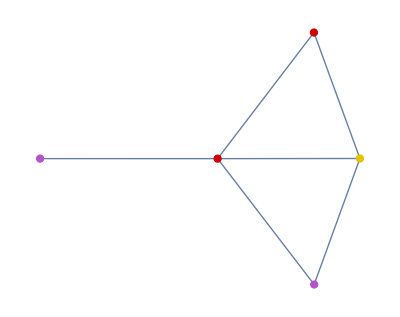

```mathematica
HighlightGraph[g,sol]
```